Set the parameters of the system:

```mathematica
omega=2Pi
omega0 = 1.5 omega
beta=omega0/4
gamma = 1.084
```

2 π

9.42478

2.35619

1.084

Solve the actual differential equation:

```mathematica
s1 = NDSolve[
{

Phi''[t]+2beta Phi'[t]+omega0^2 Sin[Phi[t]]== gamma omega0^2 Cos[omega t],

Phi[0]==0,Phi'[0]==0},Phi,{t,0,7}]
```

{{Phi→InterpolatingFunction[{{0., 7.}}, <>]}}

Solve again with a slightly different initial condition:

```mathematica
s2 = NDSolve[
{

Phi''[t]+2beta Phi'[t]+omega0^2 Sin[Phi[t]]== gamma omega0^2 Cos[omega t],

Phi[0]==0.00001,Phi'[0]==0},Phi,{t,0,7}]
```

{{Phi→InterpolatingFunction[{{0., 7.}}, <>]}}

Show logarithm of absolute difference between the solutions:

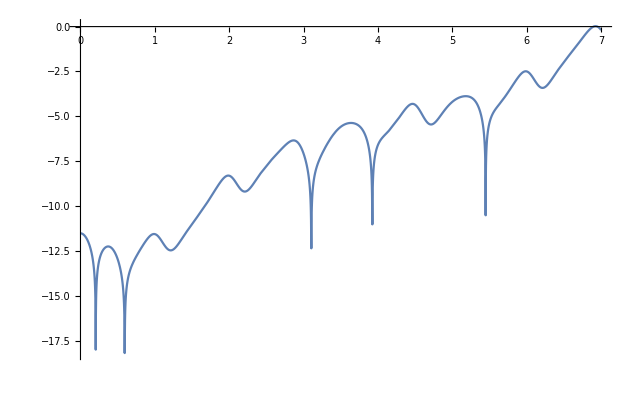

```mathematica
Plot[Log[Abs[Evaluate[Phi[t]/.s1]-Evaluate[Phi[t]/.s2]]],{t,0,7}, PlotRange -> All]
```